# QHD-2, QHD-3 and QHD-4 decay from a metastable potential

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx

## Introduction

Higher Order Quantized Hamilton Dynamics (QHD) is applied to the decay from a metastable potential. QHD gives an approximation to the Heisenberg Equations of Motion (EOM). The QHD commands used in this document are included in QUANTUM, which is a free Mathematica add-on that can be downloaded from
 http://homepage.cem.itesm.mx/lgomez/quantum/
This tutorial shows how to use the QUANTUM Mathematica add-on to reproduce the results and graphs from Pahl and Prezhdo in J. Chem Phys. Vol 116 No. 20, May 2002, Pages 8704-8712
 http://homepage.cem.itesm.mx/lgomez/quantum/QHDHigherOrders.pdf

## Load the Package

First load the Quantum`QHD` package. Write:
Needs["Quantum`QHD`"]
then press at the same time the keys ⇧-⌤ to evaluate. Mathematica will load the package and print a welcome message:

```mathematica
Needs["Quantum`QHD`"]
```

Quantum`QHD` 
A Mathematica package for Quantized Hamilton Dynamics approximation to Heisenberg Equations of Motion
by José Luis Gómez-Muñoz
based on the original idea of Kirill Igumenshchev

This add-on does NOT work properly with the debugger turned on. Therefore the debugger must NOT be checked in the Evaluation menu of Mathematica.

Execute SetQHDAliases[] in order to use the keyboard to enter QHD objects
SetQHDAliases[] must be executed again in each new notebook that is created

In order to use the keyboard to enter quantum objects write:
SetQHDAliases[ ];
then press at the same time the keys ⇧-⌤ to evaluate. Remember that SetQuantumAliases[ ] must be evaluated again in each new notebook:

```mathematica
SetQHDAliases[]
```

ALIASES:
[ESC]on[ESC]     · Quantum concatenation symbol
[ESC]time[ESC]   𝓉 Time symbol
[ESC]hb[ESC]     ℏ Reduced Planck's constant (h bar)
[ESC]ii[ESC]     ⅈ Imaginary I symbol
[ESC]inf[ESC]    ∞ Infinity symbol
[ESC]->[ESC]     → Option (Rule) symbol
[ESC]ave[ESC]    ⟨□⟩ Quantum average template
[ESC]expec[ESC]  ⟨□⟩ Quantum average template
[ESC]symm[ESC]   (□·□)_𝓈 Symmetrized quantum product template
[ESC]comm[ESC]   ⟦□,□⟧_- Commutator template
[ESC]po[ESC]     (□)^□ Power template
[ESC]su[ESC]     □_□ Subscripted variable template
[ESC]posu[ESC]   □_□^□ Power of a subscripted variable template
[ESC]fra[ESC]    □/□ Fraction template
[ESC]eva[ESC]    □/.{□→□,□→□} Evaluation (ReplaceAll) template

SetQHDAliases[] must be executed again in each new notebook that is created, only one time per notebook.

## Commutation Relationships and Hamiltonian

This Hamiltoninan and commutation relationships are those used by Pahl and Prezhdo in their paper.
In order to enter the templates and symbols ⟦□,□⟧_-, □_□, ⅈ and ℏ you can either use the QHD palette (toolbar) or, if the command SetQHDAliases[] has been executed in this Mathematica notebook, then press the keys [ESC]comm[ESC], [ESC]su[ESC], [ESC]ii[ESC] and [ESC]hb[ESC] respectively:

```mathematica
SetQuantumObject[q,p];
⟦q,p⟧_-=ⅈ*ℏ;
mh=p^2/(2m)+Subscript[a, 2]/2 q^2+Subscript[a, 3]/3 q^3
```

p^2/(2 m)+(q^2 a_2)/2+(q^3 a_3)/3

## Heisenberg Equations of Motion

The evolution of the expected value of an observable A in the Heisenberg representation is given by the equation of motion (EOM): 
 ⅈ ℏ d/dt⟨A⟩=⟨[A,H]⟩
The Heisenberg EOM can be calculated using the QHD-Mathematica command QHDEOM, as shown below. The first argument specifies the QHD-order, which is set below to ∞ so that no QHD approximation is made in this first example. The second argument is the observable, which is set to p in the example below. The third argument is the Hamiltonian, remember that it was stored in variable mh above in this document. Finally options can be included, for example QHDHBar→1 specifies that reduced Planck’s constant (Dirac constant) will take the value of 1 (The → symbol can be entered by pressing the keys [ESC]->[ESC], that is [ESC][MINUS][GREATERTHAN][ESC]). The output of QHDEOM can be stored in a variable; it is stored in meom below:

```mathematica
meom=QHDEOM[∞,p,mh]
```

{{QHDLabel,No closure was applied},{⟨p⟩,-a_2 ⟨q⟩-a_3 ⟨q^2⟩}}

The output of 	QHDEOM can be shown in a nicer format using QHDForm. The output meom that was stored above is formated that way below:

```mathematica
QHDForm[meom]
```

No closure was applied
(d⟨p⟩)/d𝓉=-a_2 ⟨q⟩-a_3 ⟨q^2⟩

On the other hand, the command QHDDifferentialEquations formats the output of QHDEOM as a standard Mathematica equation, as those that can be part of the input of standard Mathematica commands like DSolve and NDSolve. The output meom that was stored above is formated that way below:

```mathematica
QHDDifferentialEquations[meom]
```

{⟨p⟩'[𝓉]==-a_2 ⟨q⟩[𝓉]-a_3 ⟨q^2⟩[𝓉]}

A different symbol for time can be specified. The operator → can be entered pressing the keys [ESC][MINUS][GREATERTHAN][ESC], see the equations below:

```mathematica
QHDDifferentialEquations[meom,QHDSymbolForTime->z]
```

{⟨p⟩'[z]==-a_2 ⟨q⟩[z]-a_3 ⟨q^2⟩[z]}

The EOM for ⟨p⟩ depends on ⟨q⟩ and ⟨q^2⟩ (please remember that ⟨A^2⟩ is NOT the same as ⟨A⟩^2). Next, the EOMs of  ⟨q⟩ and ⟨q^2⟩ can generate new expectation values, such as ⟨p·q⟩_s=⟨(p·q+q·p)/2⟩. Regarding each expectation value as a dynamical variable, we can generate a hierarchy of EOMs, which in general is an infinite hierarchy. We can obtain some of the EOM’s of that infinite hierarchy using the QHD-Mathematica command QHDHierarchy, which has the same syntax as the command QHDEOM that was used above. Likewise, the output of QHDHierarchy can be stored in a variable (mhie in the example below) and shown using the command QHDForm below:

```mathematica
mhie=QHDHierarchy[∞,p,mh];
QHDForm[mhie]
```

Calculations were stopped at order QHDMaxOrder→2
(d⟨p⟩)/d𝓉=-a_2 ⟨q⟩-a_3 ⟨q^2⟩
(d⟨q⟩)/d𝓉=⟨p⟩/m
(d⟨q^2⟩)/d𝓉=(2 ⟨pq⟩_𝓈)/m
(d⟨pq⟩_𝓈)/d𝓉=⟨p^2⟩/m-a_2 ⟨q^2⟩-a_3 ⟨q^3⟩
(d⟨p^2⟩)/d𝓉=-2 a_2 ⟨pq⟩_𝓈-2 a_3 ⟨p q^2⟩_𝓈

A EOM hierarchy can be shown in a graph using the command QHDGraphPlot on the output of QHDHierachy. Arrows point from a first dynamical variable to a second dynamical variable that includes the first one in its EOM; please compare the table above with the graph below:

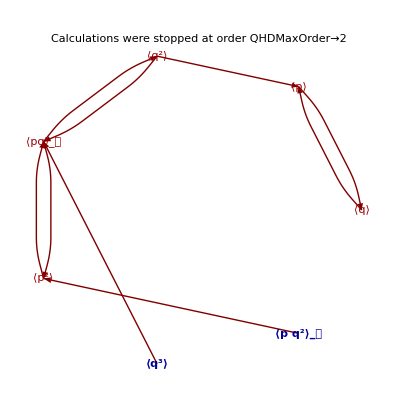

```mathematica
QHDGraphPlot[mhie]
```

## QHD-2 Closure Approximation

QHDHierarchy stops calculating infinite hierarchies as specified by its option QHDMaxOrder, which takes a default value of 2. Some of the dynamical variables (expectation values) in the truncated hierarchy will not have their equation of motion (EOM) included, as it was shown above by the colors in the ouput of QHDGraphPlot. A closure procedure has to be applied in order to approximate those dynamical variables in terms of those other variables that do have their EOMs included in the hierarchy. For instance, the approximation
⟨ABC⟩≈⟨AB⟩⟨C⟩+⟨AC⟩⟨B⟩+⟨BC⟩⟨A⟩-2⟨A⟩⟨B⟩⟨C⟩
is used to approximate the third-order dynamical variables ⟨q^3⟩ and ⟨pq^2⟩_𝓈 in terms of the firts and second order variables ⟨p⟩, ⟨q⟩, ⟨p^2⟩, ⟨q^2⟩ and ⟨p·q⟩_s=⟨(p·q+q·p)/2⟩, thus we obtain a second order QHD finite hierarchy of equations, QHD-2.
The QHD-2 hierarchy is obtained as the output of the command QHDHierarchy with the first argument set to 2. Same as above, the second argument is the first variable in the hierarchy, the third argument is the hamiltonian, and optional arguments can be given after that. The output of QHDHierarchy is stored in the variable mhier2, and it is shown using the QHDForm command below:

```mathematica
mhier2=QHDHierarchy[2,p,mh];
QHDForm[mhier2]
```

Closure procedure was applied to order 2
(d⟨p⟩)/d𝓉=-a_2 ⟨q⟩-a_3 ⟨q^2⟩
(d⟨q⟩)/d𝓉=⟨p⟩/m
(d⟨q^2⟩)/d𝓉=(2 ⟨pq⟩_𝓈)/m
(d⟨pq⟩_𝓈)/d𝓉=⟨p^2⟩/m+2 a_3 ⟨q⟩^3-a_2 ⟨q^2⟩-3 a_3 ⟨q⟩ ⟨q^2⟩
(d⟨p^2⟩)/d𝓉=4 a_3 ⟨p⟩ ⟨q⟩^2-2 a_3 ⟨p⟩ ⟨q^2⟩-2 a_2 ⟨pq⟩_𝓈-4 a_3 ⟨q⟩ ⟨pq⟩_𝓈

The closed QHD-2 hierarchy can be shown using the QHDGraphPlot command, compare the table above and the graph below:

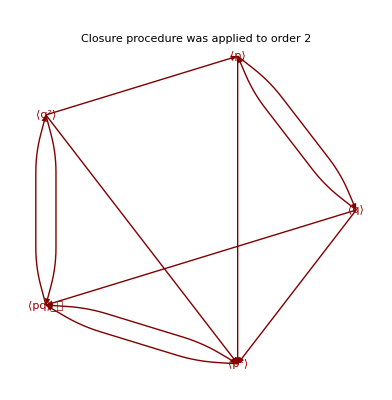

```mathematica
QHDGraphPlot[mhier2]
```

## Solution of the QHD-2 Equations: Decay from Metastable Potential

Next we evaluate the hierarchy when the parameters tkes the numerical values used by Pahl and Prezhdo in their paper, and the result of that evaluation is stored in the variable mnumhier2:

```mathematica
mnumhier2=mhier2 /.{m->1,Subscript[a, 2]->1,Subscript[a, 3]->1/2,ℏ->1};
QHDForm[mnumhier2]
```

Closure procedure was applied to order 2
(d⟨p⟩)/d𝓉=-⟨q⟩-⟨q^2⟩/2
(d⟨q⟩)/d𝓉=⟨p⟩
(d⟨q^2⟩)/d𝓉=2 ⟨pq⟩_𝓈
(d⟨pq⟩_𝓈)/d𝓉=⟨p^2⟩+⟨q⟩^3-⟨q^2⟩-3/2 ⟨q⟩ ⟨q^2⟩
(d⟨p^2⟩)/d𝓉=2 ⟨p⟩ ⟨q⟩^2-⟨p⟩ ⟨q^2⟩-2 ⟨pq⟩_𝓈-2 ⟨q⟩ ⟨pq⟩_𝓈

The command QHDInitialConditionsTemplate generates an initial conditions template for the hierarchy:

```mathematica
QHDInitialConditionsTemplate[mnumhier2,0]
```

{⟨p⟩[0]==■,⟨q⟩[0]==■,⟨q^2⟩[0]==■,⟨(p·q)_𝓈⟩[0]==■,⟨p^2⟩[0]==■}

Copy-paste the output of the previous command as input in the next one. Fill in the placeholders (■) with the appropiate initial values. Those initial values can be numbers. On the other hand, in the calculation below they are symbols like po, and then these symbols are evaluated at the desired numerical values. These initial conditions correspond to a Gaussian wavepacket,  J. Chem Phys. Vol 113 No. 20, May 2002, Pages 8704-8712
 http://homepage.cem.itesm.mx/lgomez/quantum/QHDHigherOrders.pdf
The initial conditions are stored in the variable minicond2 below:

```mathematica
minicond2=
{⟨p⟩[0]==po,⟨q⟩[0]==qo,⟨q^2⟩[0]==qo^2+ℏ/(2m*ω),⟨Subscript[(p·q), 𝓈]⟩[0]==po*qo,⟨p^2⟩[0]==po^2+(ℏ*m*ω)/2}/.{qo->0,po->0,ω->1,m->1,ℏ->1}
```

{⟨p⟩[0]==0,⟨q⟩[0]==0,⟨q^2⟩[0]==1/2,⟨(p·q)_𝓈⟩[0]==0,⟨p^2⟩[0]==1/2}

The command QHDNDSolve takes as arguments the numerical version of the hierarchy (which was stored in the variable mnumhier2), the initial conditions (which were stored in minicond2), the initial time and the final time. The output of this command is the numerical solution of the differential equations, in the form of InterpolatingFunction objects. This output can be used to plot (graph) the dynamical variables as functions of time, as it will be shown below in this document. The output is stored in the variable msol2 in the calculation below:

```mathematica
msol2=QHDNDSolve[mnumhier2,minicond2,0,6.4]
```

{{⟨p⟩→InterpolatingFunction[{{0.,6.4}},<>],⟨q⟩→InterpolatingFunction[{{0.,6.4}},<>],⟨q^2⟩→InterpolatingFunction[{{0.,6.4}},<>],⟨(p·q)_𝓈⟩→InterpolatingFunction[{{0.,6.4}},<>],⟨p^2⟩→InterpolatingFunction[{{0.,6.4}},<>]}}

The command command QHDPlot takes as its second argument the output of QHDNDSolve, which was stored in the variable msol2. The first argument specifies the dynamical variables or expression that we want to plot (graph) as a function of time, see the plot below:

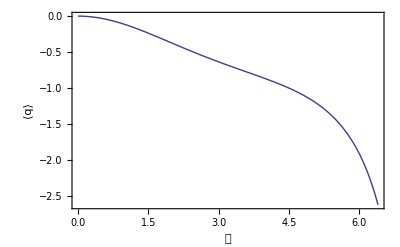

```mathematica
QHDPlot[q,msol2]
```

QHDPlot accepts the same Options as the standard Mathematica command Plot. Some of those options are used, and the plot stored in the variable mgraph2, it will be used later in this document, see the commands below:

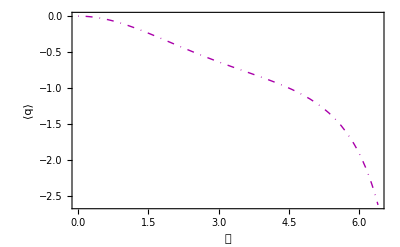

```mathematica
mgraph2=QHDPlot[q,msol2,PlotStyle->Directive[Thick,DotDashed,Darker[Magenta]]]
```

## QHD-3 Closure Approximation

The QHD-3 hierarchy for this problem can be obtained with the first argument of QHDHierarchy set to 3. This calculation takes several seconds in a laptop computer, the result is stored in the variable mhier3 below:

```mathematica
mhier3=QHDHierarchy[3,p,mh];
QHDForm[mhier3]
```

Closure procedure was applied to order 3
(d⟨p⟩)/d𝓉=-a_2 ⟨q⟩-a_3 ⟨q^2⟩
(d⟨q⟩)/d𝓉=⟨p⟩/m
(d⟨q^2⟩)/d𝓉=(2 ⟨pq⟩_𝓈)/m
(d⟨pq⟩_𝓈)/d𝓉=⟨p^2⟩/m-a_2 ⟨q^2⟩-a_3 ⟨q^3⟩
(d⟨p^2⟩)/d𝓉=-2 a_2 ⟨pq⟩_𝓈-2 a_3 ⟨p q^2⟩_𝓈
(d⟨q^3⟩)/d𝓉=(3 ⟨p q^2⟩_𝓈)/m
(d⟨p q^2⟩_𝓈)/d𝓉=-6 a_3 ⟨q⟩^4+12 a_3 ⟨q⟩^2 ⟨q^2⟩-3 a_3 ⟨q^2⟩^2-a_2 ⟨q^3⟩-4 a_3 ⟨q⟩ ⟨q^3⟩+(2 ⟨p^2 q⟩_𝓈)/m
(d⟨p^2 q⟩_𝓈)/d𝓉=⟨p^3⟩/m-12 a_3 ⟨p⟩ ⟨q⟩^3+12 a_3 ⟨p⟩ ⟨q⟩ ⟨q^2⟩-2 a_3 ⟨p⟩ ⟨q^3⟩+12 a_3 ⟨q⟩^2 ⟨pq⟩_𝓈-6 a_3 ⟨q^2⟩ ⟨pq⟩_𝓈-2 a_2 ⟨p q^2⟩_𝓈-6 a_3 ⟨q⟩ ⟨p q^2⟩_𝓈
(d⟨p^3⟩)/d𝓉=(ℏ^2 a_3)/2-18 a_3 ⟨p⟩^2 ⟨q⟩^2+6 a_3 ⟨p^2⟩ ⟨q⟩^2+6 a_3 ⟨p⟩^2 ⟨q^2⟩-3 a_3 ⟨p^2⟩ ⟨q^2⟩+24 a_3 ⟨p⟩ ⟨q⟩ ⟨pq⟩_𝓈-6 a_3 ⟨pq⟩_𝓈^2-3 a_2 ⟨p^2 q⟩_𝓈-6 a_3 ⟨q⟩ ⟨p^2 q⟩_𝓈-6 a_3 ⟨p⟩ ⟨p q^2⟩_𝓈

The products above are symmetrized, for instance ⟨p·q^2⟩_s=⟨(p·q^2+q^2·p)/2⟩
The QHD-3 hierarchy can be shown using the QHDGraphPlot command, compare the table above and the graph below:

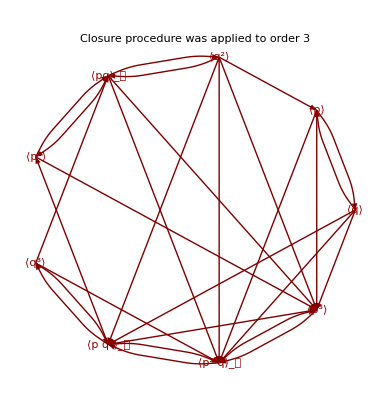

```mathematica
QHDGraphPlot[mhier3]
```

## Solution of the QHD-3 Equations

Next we evaluate the hierarchy when the parameters tkes the numerical values used by Pahl and Prezhdo in their paper, and the result of that evaluation is stored in the variable mnumhier3:

```mathematica
mnumhier3=mhier3 /.{m->1,Subscript[a, 2]->1,Subscript[a, 3]->1/2,ℏ->1};
QHDForm[mnumhier3]
```

Closure procedure was applied to order 3
(d⟨p⟩)/d𝓉=-⟨q⟩-⟨q^2⟩/2
(d⟨q⟩)/d𝓉=⟨p⟩
(d⟨q^2⟩)/d𝓉=2 ⟨pq⟩_𝓈
(d⟨pq⟩_𝓈)/d𝓉=⟨p^2⟩-⟨q^2⟩-⟨q^3⟩/2
(d⟨p^2⟩)/d𝓉=-2 ⟨pq⟩_𝓈-⟨p q^2⟩_𝓈
(d⟨q^3⟩)/d𝓉=3 ⟨p q^2⟩_𝓈
(d⟨p q^2⟩_𝓈)/d𝓉=-3 ⟨q⟩^4+6 ⟨q⟩^2 ⟨q^2⟩-(3 ⟨q^2⟩^2)/2-⟨q^3⟩-2 ⟨q⟩ ⟨q^3⟩+2 ⟨p^2 q⟩_𝓈
(d⟨p^2 q⟩_𝓈)/d𝓉=⟨p^3⟩-6 ⟨p⟩ ⟨q⟩^3+6 ⟨p⟩ ⟨q⟩ ⟨q^2⟩-⟨p⟩ ⟨q^3⟩+6 ⟨q⟩^2 ⟨pq⟩_𝓈-3 ⟨q^2⟩ ⟨pq⟩_𝓈-2 ⟨p q^2⟩_𝓈-3 ⟨q⟩ ⟨p q^2⟩_𝓈
(d⟨p^3⟩)/d𝓉=1/4-9 ⟨p⟩^2 ⟨q⟩^2+3 ⟨p^2⟩ ⟨q⟩^2+3 ⟨p⟩^2 ⟨q^2⟩-3/2 ⟨p^2⟩ ⟨q^2⟩+12 ⟨p⟩ ⟨q⟩ ⟨pq⟩_𝓈-3 ⟨pq⟩_𝓈^2-3 ⟨p^2 q⟩_𝓈-3 ⟨q⟩ ⟨p^2 q⟩_𝓈-3 ⟨p⟩ ⟨p q^2⟩_𝓈

The command QHDInitialConditionsTemplate generates an initial conditions template for the hierarchy:

```mathematica
QHDInitialConditionsTemplate[mnumhier3,0]
```

{⟨p⟩[0]==■,⟨q⟩[0]==■,⟨q^2⟩[0]==■,⟨(p·q)_𝓈⟩[0]==■,⟨p^2⟩[0]==■,⟨q^3⟩[0]==■,⟨(p·q^2)_𝓈⟩[0]==■,⟨(p^2·q)_𝓈⟩[0]==■,⟨p^3⟩[0]==■}

Copy-paste the output of the previous command as input in the next one. Fill in the placeholders (■) with the appropiate initial values. Those initial values can be numbers. On the other hand, in the calculation below they are symbols like po, and then these symbols are evaluated at the desired numerical values. These initial conditions correspond to a Gaussian wavepacket,  J. Chem Phys. Vol 113 No. 20, May 2002, Pages 8704-8712
 http://homepage.cem.itesm.mx/lgomez/quantum/QHDHigherOrders.pdf
The initial conditions are stored in the variable minicond3 below:

```mathematica
minicond3=
{⟨p⟩[0]==po,⟨q⟩[0]==qo,⟨q^2⟩[0]==qo^2+ℏ/(2m*ω),⟨Subscript[(p·q), 𝓈]⟩[0]==po*qo,⟨p^2⟩[0]==po^2+(ℏ*m*ω)/2,⟨q^3⟩[0]==qo^3+3/2 qo ℏ/(m*ω),⟨Subscript[(p·q^2), 𝓈]⟩[0]==po*qo^2+1/2 po ℏ/(m*ω),⟨Subscript[(p^2·q), 𝓈]⟩[0]==po^2*qo+1/2 qo*ℏ*m*ω,⟨p^3⟩[0]==po^3+3/2 po*ℏ*m*ω}/.{qo->0,po->0,ω->1,m->1,ℏ->1}
```

{⟨p⟩[0]==0,⟨q⟩[0]==0,⟨q^2⟩[0]==1/2,⟨(p·q)_𝓈⟩[0]==0,⟨p^2⟩[0]==1/2,⟨q^3⟩[0]==0,⟨(p·q^2)_𝓈⟩[0]==0,⟨(p^2·q)_𝓈⟩[0]==0,⟨p^3⟩[0]==0}

The command QHDNDSolve takes as arguments the numerical version of the hierarchy (which was stored in the variable mnumhier3), the initial conditions (which were stored in minicond3), the initial time and the final time. The output of this command is the numerical solution of the differential equations, in the form of InterpolatingFunction objects. This output can be used to plot (graph) the dynamical variables as functions of time, as it will be shown below in this document. The output is stored in the variable msol3 in the calculation below:

```mathematica
msol3=QHDNDSolve[mnumhier3,minicond3,0,4.6]
```

{{⟨p⟩→InterpolatingFunction[{{0.,4.6}},<>],⟨q⟩→InterpolatingFunction[{{0.,4.6}},<>],⟨q^2⟩→InterpolatingFunction[{{0.,4.6}},<>],⟨(p·q)_𝓈⟩→InterpolatingFunction[{{0.,4.6}},<>],⟨p^2⟩→InterpolatingFunction[{{0.,4.6}},<>],⟨q^3⟩→InterpolatingFunction[{{0.,4.6}},<>],⟨(p·q^2)_𝓈⟩→InterpolatingFunction[{{0.,4.6}},<>],⟨(p^2·q)_𝓈⟩→InterpolatingFunction[{{0.,4.6}},<>],⟨p^3⟩→InterpolatingFunction[{{0.,4.6}},<>]}}

The command command QHDPlot takes as its second argument the output of QHDNDSolve, which was stored in the variable msol3. The first argument specifies the dynamical variables or expression that we want to plot (graph) as a function of time, see the plot below:

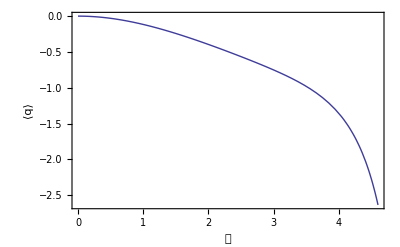

```mathematica
QHDPlot[q,msol3]
```

QHDPlot accepts the same Options as the standard Mathematica command Plot. Some of those options are used, and the plot stored in the variable mgraph3, it will be used later in this document, see the commands below:

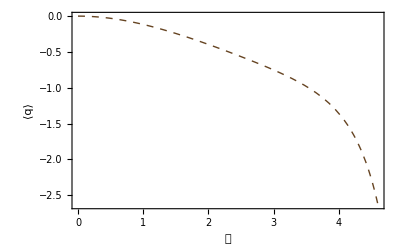

```mathematica
mgraph3=QHDPlot[q,msol3,PlotStyle->Directive[Thick,Dashed,Darker[Brown]]]
```

The standard Mathematica command Show can be used to compare mgraph3, which was stored above, and mgraph2, which was stored in a previous section. The paper by Pahl and Prezhdo shows that QHD-3 is a better approximation to Quantum Mechanics than QHD-2, see the graph below:

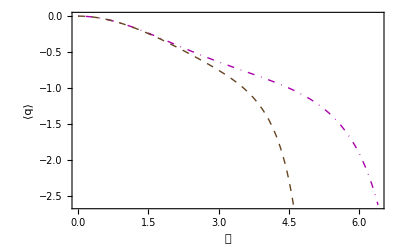

```mathematica
Show[mgraph2,mgraph3]
```

## QHD-4 Closure Approximation

The QHD-4 hierarchy for this problem can be obtained with the first argument of QHDHierarchy set to 4. This calculation takes several minutes in a laptop computer; the result is stored in the variable mhier4 below:

```mathematica
mhier4=QHDHierarchy[4,p,mh];
QHDForm[mhier4]
```

Closure procedure was applied to order 4
(d⟨p⟩)/d𝓉=-a_2 ⟨q⟩-a_3 ⟨q^2⟩
(d⟨q⟩)/d𝓉=⟨p⟩/m
(d⟨q^2⟩)/d𝓉=(2 ⟨pq⟩_𝓈)/m
(d⟨pq⟩_𝓈)/d𝓉=⟨p^2⟩/m-a_2 ⟨q^2⟩-a_3 ⟨q^3⟩
(d⟨p^2⟩)/d𝓉=-2 a_2 ⟨pq⟩_𝓈-2 a_3 ⟨p q^2⟩_𝓈
(d⟨q^3⟩)/d𝓉=(3 ⟨p q^2⟩_𝓈)/m
(d⟨p q^2⟩_𝓈)/d𝓉=-a_2 ⟨q^3⟩-a_3 ⟨q^4⟩+(2 ⟨p^2 q⟩_𝓈)/m
(d⟨q^4⟩)/d𝓉=(4 ⟨p q^3⟩_𝓈)/m
(d⟨p^2 q⟩_𝓈)/d𝓉=⟨p^3⟩/m-2 a_2 ⟨p q^2⟩_𝓈-2 a_3 ⟨p q^3⟩_𝓈
(d⟨p q^3⟩_𝓈)/d𝓉=(3 ℏ^2)/(2 m)+24 a_3 ⟨q⟩^5-60 a_3 ⟨q⟩^3 ⟨q^2⟩+30 a_3 ⟨q⟩ ⟨q^2⟩^2+20 a_3 ⟨q⟩^2 ⟨q^3⟩-10 a_3 ⟨q^2⟩ ⟨q^3⟩-a_2 ⟨q^4⟩-5 a_3 ⟨q⟩ ⟨q^4⟩+(3 ⟨p^2 q^2⟩_𝓈)/m
(d⟨p^3⟩)/d𝓉=-ℏ^2 a_3-3 a_2 ⟨p^2 q⟩_𝓈-3 a_3 ⟨p^2 q^2⟩_𝓈
(d⟨p^2 q^2⟩_𝓈)/d𝓉=48 a_3 ⟨p⟩ ⟨q⟩^4-72 a_3 ⟨p⟩ ⟨q⟩^2 ⟨q^2⟩+12 a_3 ⟨p⟩ ⟨q^2⟩^2+16 a_3 ⟨p⟩ ⟨q⟩ ⟨q^3⟩-2 a_3 ⟨p⟩ ⟨q^4⟩-48 a_3 ⟨q⟩^3 ⟨pq⟩_𝓈+48 a_3 ⟨q⟩ ⟨q^2⟩ ⟨pq⟩_𝓈-8 a_3 ⟨q^3⟩ ⟨pq⟩_𝓈+(2 ⟨p^3 q⟩_𝓈)/m+24 a_3 ⟨q⟩^2 ⟨p q^2⟩_𝓈-12 a_3 ⟨q^2⟩ ⟨p q^2⟩_𝓈-2 a_2 ⟨p q^3⟩_𝓈-8 a_3 ⟨q⟩ ⟨p q^3⟩_𝓈
(d⟨p^3 q⟩_𝓈)/d𝓉=-3/2 ℏ^2 a_2+⟨p^4⟩/m-4 ℏ^2 a_3 ⟨q⟩+72 a_3 ⟨p⟩^2 ⟨q⟩^3-18 a_3 ⟨p^2⟩ ⟨q⟩^3-54 a_3 ⟨p⟩^2 ⟨q⟩ ⟨q^2⟩+18 a_3 ⟨p^2⟩ ⟨q⟩ ⟨q^2⟩+6 a_3 ⟨p⟩^2 ⟨q^3⟩-3 a_3 ⟨p^2⟩ ⟨q^3⟩-108 a_3 ⟨p⟩ ⟨q⟩^2 ⟨pq⟩_𝓈+36 a_3 ⟨p⟩ ⟨q^2⟩ ⟨pq⟩_𝓈+36 a_3 ⟨q⟩ ⟨pq⟩_𝓈^2+18 a_3 ⟨q⟩^2 ⟨p^2 q⟩_𝓈-9 a_3 ⟨q^2⟩ ⟨p^2 q⟩_𝓈+36 a_3 ⟨p⟩ ⟨q⟩ ⟨p q^2⟩_𝓈-18 a_3 ⟨pq⟩_𝓈 ⟨p q^2⟩_𝓈-3 a_2 ⟨p^2 q^2⟩_𝓈-9 a_3 ⟨q⟩ ⟨p^2 q^2⟩_𝓈-6 a_3 ⟨p⟩ ⟨p q^3⟩_𝓈
(d⟨p^4⟩)/d𝓉=-4 ℏ^2 a_3 ⟨p⟩+96 a_3 ⟨p⟩^3 ⟨q⟩^2-72 a_3 ⟨p⟩ ⟨p^2⟩ ⟨q⟩^2+8 a_3 ⟨p^3⟩ ⟨q⟩^2-24 a_3 ⟨p⟩^3 ⟨q^2⟩+24 a_3 ⟨p⟩ ⟨p^2⟩ ⟨q^2⟩-4 a_3 ⟨p^3⟩ ⟨q^2⟩-144 a_3 ⟨p⟩^2 ⟨q⟩ ⟨pq⟩_𝓈+48 a_3 ⟨p^2⟩ ⟨q⟩ ⟨pq⟩_𝓈+48 a_3 ⟨p⟩ ⟨pq⟩_𝓈^2+48 a_3 ⟨p⟩ ⟨q⟩ ⟨p^2 q⟩_𝓈-24 a_3 ⟨pq⟩_𝓈 ⟨p^2 q⟩_𝓈-4 a_2 ⟨p^3 q⟩_𝓈-8 a_3 ⟨q⟩ ⟨p^3 q⟩_𝓈+24 a_3 ⟨p⟩^2 ⟨p q^2⟩_𝓈-12 a_3 ⟨p^2⟩ ⟨p q^2⟩_𝓈-12 a_3 ⟨p⟩ ⟨p^2 q^2⟩_𝓈

The products above are symmetrized, for instance ⟨p·q^2⟩_s=⟨(p·q^2+q^2·p)/2⟩
The QHD-4 hierarchy can be shown using the QHDGraphPlot command, compare the table above and the graph below:

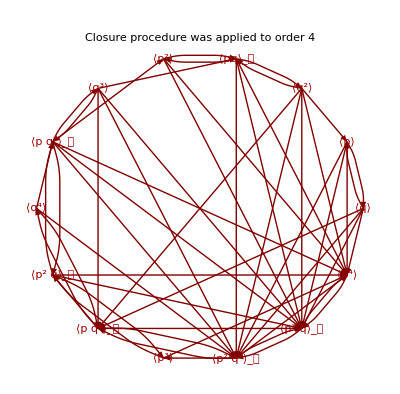

```mathematica
QHDGraphPlot[mhier4]
```

## Solution of the QHD-4 Equations

Next we evaluate the hierarchy when the parameters tkes the numerical values used by Pahl and Prezhdo in their paper, and the result of that evaluation is stored in the variable mnumhier4:

```mathematica
mnumhier4=mhier4 /.{m->1,Subscript[a, 2]->1,Subscript[a, 3]->1/2,ℏ->1};
QHDForm[mnumhier4]
```

Closure procedure was applied to order 4
(d⟨p⟩)/d𝓉=-⟨q⟩-⟨q^2⟩/2
(d⟨q⟩)/d𝓉=⟨p⟩
(d⟨q^2⟩)/d𝓉=2 ⟨pq⟩_𝓈
(d⟨pq⟩_𝓈)/d𝓉=⟨p^2⟩-⟨q^2⟩-⟨q^3⟩/2
(d⟨p^2⟩)/d𝓉=-2 ⟨pq⟩_𝓈-⟨p q^2⟩_𝓈
(d⟨q^3⟩)/d𝓉=3 ⟨p q^2⟩_𝓈
(d⟨p q^2⟩_𝓈)/d𝓉=-⟨q^3⟩-⟨q^4⟩/2+2 ⟨p^2 q⟩_𝓈
(d⟨q^4⟩)/d𝓉=4 ⟨p q^3⟩_𝓈
(d⟨p^2 q⟩_𝓈)/d𝓉=⟨p^3⟩-2 ⟨p q^2⟩_𝓈-⟨p q^3⟩_𝓈
(d⟨p q^3⟩_𝓈)/d𝓉=3/2+12 ⟨q⟩^5-30 ⟨q⟩^3 ⟨q^2⟩+15 ⟨q⟩ ⟨q^2⟩^2+10 ⟨q⟩^2 ⟨q^3⟩-5 ⟨q^2⟩ ⟨q^3⟩-⟨q^4⟩-5/2 ⟨q⟩ ⟨q^4⟩+3 ⟨p^2 q^2⟩_𝓈
(d⟨p^3⟩)/d𝓉=-1/2-3 ⟨p^2 q⟩_𝓈-3/2 ⟨p^2 q^2⟩_𝓈
(d⟨p^2 q^2⟩_𝓈)/d𝓉=24 ⟨p⟩ ⟨q⟩^4-36 ⟨p⟩ ⟨q⟩^2 ⟨q^2⟩+6 ⟨p⟩ ⟨q^2⟩^2+8 ⟨p⟩ ⟨q⟩ ⟨q^3⟩-⟨p⟩ ⟨q^4⟩-24 ⟨q⟩^3 ⟨pq⟩_𝓈+24 ⟨q⟩ ⟨q^2⟩ ⟨pq⟩_𝓈-4 ⟨q^3⟩ ⟨pq⟩_𝓈+2 ⟨p^3 q⟩_𝓈+12 ⟨q⟩^2 ⟨p q^2⟩_𝓈-6 ⟨q^2⟩ ⟨p q^2⟩_𝓈-2 ⟨p q^3⟩_𝓈-4 ⟨q⟩ ⟨p q^3⟩_𝓈
(d⟨p^3 q⟩_𝓈)/d𝓉=-3/2+⟨p^4⟩-2 ⟨q⟩+36 ⟨p⟩^2 ⟨q⟩^3-9 ⟨p^2⟩ ⟨q⟩^3-27 ⟨p⟩^2 ⟨q⟩ ⟨q^2⟩+9 ⟨p^2⟩ ⟨q⟩ ⟨q^2⟩+3 ⟨p⟩^2 ⟨q^3⟩-3/2 ⟨p^2⟩ ⟨q^3⟩-54 ⟨p⟩ ⟨q⟩^2 ⟨pq⟩_𝓈+18 ⟨p⟩ ⟨q^2⟩ ⟨pq⟩_𝓈+18 ⟨q⟩ ⟨pq⟩_𝓈^2+9 ⟨q⟩^2 ⟨p^2 q⟩_𝓈-9/2 ⟨q^2⟩ ⟨p^2 q⟩_𝓈+18 ⟨p⟩ ⟨q⟩ ⟨p q^2⟩_𝓈-9 ⟨pq⟩_𝓈 ⟨p q^2⟩_𝓈-3 ⟨p^2 q^2⟩_𝓈-9/2 ⟨q⟩ ⟨p^2 q^2⟩_𝓈-3 ⟨p⟩ ⟨p q^3⟩_𝓈
(d⟨p^4⟩)/d𝓉=-2 ⟨p⟩+48 ⟨p⟩^3 ⟨q⟩^2-36 ⟨p⟩ ⟨p^2⟩ ⟨q⟩^2+4 ⟨p^3⟩ ⟨q⟩^2-12 ⟨p⟩^3 ⟨q^2⟩+12 ⟨p⟩ ⟨p^2⟩ ⟨q^2⟩-2 ⟨p^3⟩ ⟨q^2⟩-72 ⟨p⟩^2 ⟨q⟩ ⟨pq⟩_𝓈+24 ⟨p^2⟩ ⟨q⟩ ⟨pq⟩_𝓈+24 ⟨p⟩ ⟨pq⟩_𝓈^2+24 ⟨p⟩ ⟨q⟩ ⟨p^2 q⟩_𝓈-12 ⟨pq⟩_𝓈 ⟨p^2 q⟩_𝓈-4 ⟨p^3 q⟩_𝓈-4 ⟨q⟩ ⟨p^3 q⟩_𝓈+12 ⟨p⟩^2 ⟨p q^2⟩_𝓈-6 ⟨p^2⟩ ⟨p q^2⟩_𝓈-6 ⟨p⟩ ⟨p^2 q^2⟩_𝓈

The command QHDInitialConditionsTemplate generates an initial conditions template for the hierarchy:

```mathematica
QHDInitialConditionsTemplate[mnumhier4,0]
```

{⟨p⟩[0]==■,⟨q⟩[0]==■,⟨q^2⟩[0]==■,⟨(p·q)_𝓈⟩[0]==■,⟨p^2⟩[0]==■,⟨q^3⟩[0]==■,⟨(p·q^2)_𝓈⟩[0]==■,⟨q^4⟩[0]==■,⟨(p^2·q)_𝓈⟩[0]==■,⟨(p·q^3)_𝓈⟩[0]==■,⟨p^3⟩[0]==■,⟨(p^2·q^2)_𝓈⟩[0]==■,⟨(p^3·q)_𝓈⟩[0]==■,⟨p^4⟩[0]==■}

Copy-paste the output of the previous command as input in the next one. Fill in the placeholders (■) with the appropiate initial values. Those initial values can be numbers. On the other hand, in the calculation below they are symbols like po, and then these symbols are evaluated at the desired numerical values. These initial conditions correspond to a Gaussian wavepacket,  J. Chem Phys. Vol 113 No. 20, May 2002, Pages 8704-8712
 http://homepage.cem.itesm.mx/lgomez/quantum/QHDHigherOrders.pdf
The initial conditions are stored in the variable minicond4 below:

```mathematica
minicond4=
{⟨p⟩[0]==po,⟨q⟩[0]==qo,⟨q^2⟩[0]==qo^2+ℏ/(2m*ω),⟨Subscript[(p·q), 𝓈]⟩[0]==po*qo,⟨p^2⟩[0]==po^2+(ℏ*m*ω)/2,⟨q^3⟩[0]==qo^3+3/2 qo ℏ/(m*ω),⟨Subscript[(p·q^2), 𝓈]⟩[0]==po*qo^2+1/2 po ℏ/(m*ω),⟨q^4⟩[0]==qo^4+3 qo^2 ℏ/(m*ω)+3/4(ℏ/(m*ω))^2,⟨Subscript[(p^2·q), 𝓈]⟩[0]==po^2*qo+1/2 qo*ℏ*m*ω,⟨Subscript[(p·q^3), 𝓈]⟩[0]==po*qo^3+3/2 po*qo*ℏ/(m*ω),⟨p^3⟩[0]==po^3+3/2 po*ℏ*m*ω,⟨Subscript[(p^2·q^2), 𝓈]⟩[0]==po^2*qo^2+1/2 po^2 ℏ/(m*ω)+(qo^2*ℏ*m*ω)/2-ℏ^2/4,⟨Subscript[(p^3·q), 𝓈]⟩[0]==po^3*qo+3/2 po*qo*ℏ*m*ω,⟨p^4⟩[0]==po^4+3 po^2*ℏ*m*ω+3/4(ℏ*m*ω)^2}/.{qo->0,po->0,ω->1,m->1,ℏ->1}
```

{⟨p⟩[0]==0,⟨q⟩[0]==0,⟨q^2⟩[0]==1/2,⟨(p·q)_𝓈⟩[0]==0,⟨p^2⟩[0]==1/2,⟨q^3⟩[0]==0,⟨(p·q^2)_𝓈⟩[0]==0,⟨q^4⟩[0]==3/4,⟨(p^2·q)_𝓈⟩[0]==0,⟨(p·q^3)_𝓈⟩[0]==0,⟨p^3⟩[0]==0,⟨(p^2·q^2)_𝓈⟩[0]==-1/4,⟨(p^3·q)_𝓈⟩[0]==0,⟨p^4⟩[0]==3/4}

The command QHDNDSolve takes as arguments the numerical version of the hierarchy (which was stored in the variable mnumhier4), the initial conditions (which were stored in minicond4), the initial time and the final time. The output of this command is the numerical solution of the differential equations, in the form of InterpolatingFunction objects. This output can be used to plot (graph) the dynamical variables as functions of time, as it will be shown below in this document. The output is stored in the variable msol4 in the calculation below:

```mathematica
msol4=QHDNDSolve[mnumhier4,minicond4,0,4]
```

{{⟨p⟩→InterpolatingFunction[{{0.,4.}},<>],⟨q⟩→InterpolatingFunction[{{0.,4.}},<>],⟨q^2⟩→InterpolatingFunction[{{0.,4.}},<>],⟨(p·q)_𝓈⟩→InterpolatingFunction[{{0.,4.}},<>],⟨p^2⟩→InterpolatingFunction[{{0.,4.}},<>],⟨q^3⟩→InterpolatingFunction[{{0.,4.}},<>],⟨(p·q^2)_𝓈⟩→InterpolatingFunction[{{0.,4.}},<>],⟨q^4⟩→InterpolatingFunction[{{0.,4.}},<>],⟨(p^2·q)_𝓈⟩→InterpolatingFunction[{{0.,4.}},<>],⟨(p·q^3)_𝓈⟩→InterpolatingFunction[{{0.,4.}},<>],⟨p^3⟩→InterpolatingFunction[{{0.,4.}},<>],⟨(p^2·q^2)_𝓈⟩→InterpolatingFunction[{{0.,4.}},<>],⟨(p^3·q)_𝓈⟩→InterpolatingFunction[{{0.,4.}},<>],⟨p^4⟩→InterpolatingFunction[{{0.,4.}},<>]}}

The command command QHDPlot takes as its second argument the output of QHDNDSolve, which was stored in the variable msol4. The first argument specifies the dynamical variables or expression that we want to plot (graph) as a function of time, see the plot below:

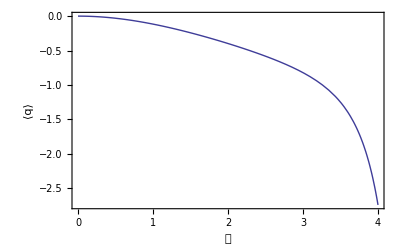

```mathematica
QHDPlot[q,msol4]
```

The command command QHDPlot takes as its second argument the output of QHDNDSolve, which was stored in the variable msol4. The first argument specifies the dynamical variables or expression that we want to plot (graph) as a function of time, see the plot below:

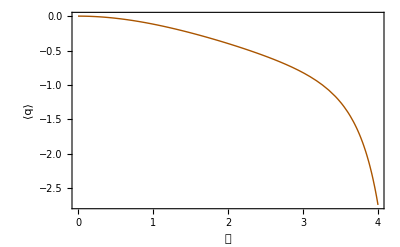

```mathematica
mgraph4=QHDPlot[q,msol4,PlotStyle->Darker[Orange]]
```

The standard Mathematica command Show can be used to compare mgraph4, which was stored above, with mgraph3 and mgraph2, which were calculated in previous sections. The paper by Pahl and Prezhdo shows that QHD-4 is a better approximation to Quantum Mechanics than QHD-3 and QHD-2, see the graph below:

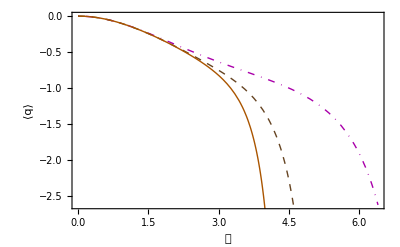

```mathematica
Show[mgraph2,mgraph3,mgraph4]
```

Standard Mathematica options can be used so that the graph looks like the corresponding graph in Pahl and Prezhdo paper, see the result below:

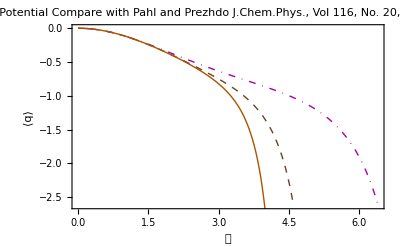

```mathematica
Show[mgraph2,mgraph3,mgraph4,
Axes->True,AxesOrigin->{0,-2},PlotLabel->"Decay from Metastable Potential\n Compare with Pahl and Prezhdo\n J.Chem.Phys., Vol 116, No. 20, May 2002\n Pages 8704-8712 Fig 3"]
```

## Saving the QHD hierarchies for future use

The calculation QHD hierarchies is time consuming, therefore it is a good idea to save them for future use. The simplest way to do it is using the standard Mathematica command Put. The QHD-2 hierarchy is stored in the file qhd2.m, see the command below:

```mathematica
Put[mhier2,"qhd2.m"]
```

The QHD-3 hierarchy is stored in the file qhd3.m, see the command below:

```mathematica
Put[mhier3,"qhd3.m"]
```

The QHD-4 hierarchy is stored in the file qhd4.m, see the command below:

```mathematica
Put[mhier4,"qhd4.m"]
```

The command FileNames[“*.m”] can be used to see the files that were created by the command Put (together with any other preexisting file with .m extension), see the command below:

```mathematica
FileNames["*.m"]
```

{hier4.m,HierarchyWater.m,qhd2.m,qhd3.m,qhd4.m,schrodingersolbarrier.m}

## Dependence of Decay Time on ℏ

Next commands have been written as they would be used in a different Mathematica session, using the command Get to load the hierarchy that was saved above (instead of calculating it again). Notice that the commutation relation and the Hamiltonian are defined again, and its important to use those that correspond to the hierarchy that is loaded. Next commands calculate and graph the dependence of decay time on ℏ, the result is stored in the variable data2, which will be used later to reproduce a graph of the paper by Pahl and Prezhdo, see the graph below:

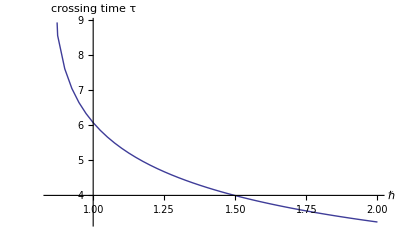

```mathematica
Needs["Quantum`QHD`"];
SetQuantumObject[q,p];
⟦q,p⟧_-=ⅈ*ℏ;
mh=p^2/(2m)+Subscript[a, 2]/2 q^2+Subscript[a, 3]/3 q^3;
hhier2=Get["qhd2.m"];
iniguess=15;
data2=Table[
hnumhier2=hhier2/.{m->1,Subscript[a, 2]->1,Subscript[a, 3]->1/2,ℏ->h};
hinicond2={⟨p⟩[0]==po,⟨q⟩[0]==qo,⟨q^2⟩[0]==qo^2+ℏ/(2m*ω),⟨Subscript[(p·q), 𝓈]⟩[0]==po*qo,⟨p^2⟩[0]==po^2+(ℏ*m*ω)/2}/.{qo->0,po->0,ω->1,m->1,ℏ->h};
hsol2=QHDNDSolve[hnumhier2,hinicond2,0,iniguess+0.5];
hqf2=QHDFunction[q,hsol2];
htime=(ht/.FindRoot[hqf2[ht]==-2,{ht,iniguess},AccuracyGoal->3,PrecisionGoal->3,MaxIterations->1000]);
iniguess=htime;
{h,htime},
{h,0.85,2,0.025}];
ListLinePlot[data2,AxesLabel->{Style[ℏ,Large],"crossing time τ"}]
```

Below we have the same calculation as above, but with QHD-3 instead of QHD-2, using the “qhd3.m” file, and storing the result in data3:

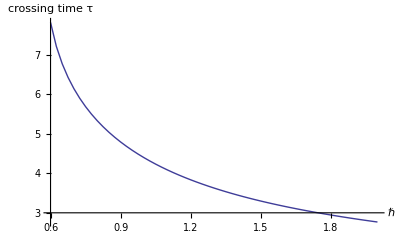

```mathematica
Needs["Quantum`QHD`"];
SetQuantumObject[q,p];
⟦q,p⟧_-=ⅈ*ℏ;
mh=p^2/(2m)+Subscript[a, 2]/2 q^2+Subscript[a, 3]/3 q^3;
hhier3=Get["qhd3.m"];
iniguess=8;
data3=Table[
hnumhier3=hhier3/.{m->1,Subscript[a, 2]->1,Subscript[a, 3]->1/2,ℏ->h};
hinicond3={⟨p⟩[0]==po,⟨q⟩[0]==qo,⟨q^2⟩[0]==qo^2+ℏ/(2m*ω),⟨Subscript[(p·q), 𝓈]⟩[0]==po*qo,⟨p^2⟩[0]==po^2+(ℏ*m*ω)/2,⟨q^3⟩[0]==qo^3+3/2 qo ℏ/(m*ω),⟨Subscript[(p·q^2), 𝓈]⟩[0]==po*qo^2+1/2 po ℏ/(m*ω),⟨Subscript[(p^2·q), 𝓈]⟩[0]==po^2*qo+1/2 qo*ℏ*m*ω,⟨p^3⟩[0]==po^3+3/2 po*ℏ*m*ω}/.{qo->0,po->0,ω->1,m->1,ℏ->h};
hsol3=QHDNDSolve[hnumhier3,hinicond3,0,iniguess+0.5];
hqf3=QHDFunction[q,hsol3];
htime=(ht/.FindRoot[hqf3[ht]==-2,{ht,iniguess},AccuracyGoal->3,PrecisionGoal->3,MaxIterations->1000]);
iniguess=htime;
{h,htime},
{h,0.6,2,0.025}];
ListLinePlot[data3,AxesLabel->{Style[ℏ,Large],"crossing time τ"}]
```

Below we have the same calculation as above, but with QHD-4 instead of QHD-3 or QHD-2, using the “qhd4.m” file, and storing the result in data4:

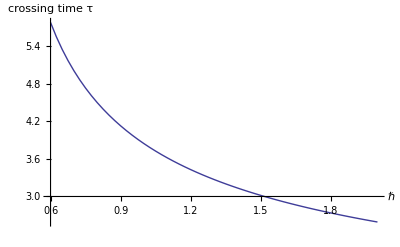

```mathematica
Needs["Quantum`QHD`"];
SetQuantumObject[q,p];
⟦q,p⟧_-=ⅈ*ℏ;
mh=p^2/(2m)+Subscript[a, 2]/2 q^2+Subscript[a, 3]/3 q^3;
hhier4=Get["qhd4.m"];
iniguess=6;
data4=Table[
hnumhier4=hhier4/.{m->1,Subscript[a, 2]->1,Subscript[a, 3]->1/2,ℏ->h};
hinicond4={⟨p⟩[0]==po,⟨q⟩[0]==qo,⟨q^2⟩[0]==qo^2+ℏ/(2m*ω),⟨Subscript[(p·q), 𝓈]⟩[0]==po*qo,⟨p^2⟩[0]==po^2+(ℏ*m*ω)/2,⟨q^3⟩[0]==qo^3+3/2 qo ℏ/(m*ω),⟨Subscript[(p·q^2), 𝓈]⟩[0]==po*qo^2+1/2 po ℏ/(m*ω),⟨q^4⟩[0]==qo^4+3 qo^2 ℏ/(m*ω)+3/4(ℏ/(m*ω))^2,⟨Subscript[(p^2·q), 𝓈]⟩[0]==po^2*qo+1/2 qo*ℏ*m*ω,⟨Subscript[(p·q^3), 𝓈]⟩[0]==po*qo^3+3/2 po*qo*ℏ/(m*ω),⟨p^3⟩[0]==po^3+3/2 po*ℏ*m*ω,⟨Subscript[(p^2·q^2), 𝓈]⟩[0]==po^2*qo^2+1/2 po^2 ℏ/(m*ω)+(qo^2*ℏ*m*ω)/2-ℏ^2/4,⟨Subscript[(p^3·q), 𝓈]⟩[0]==po^3*qo+3/2 po*qo*ℏ*m*ω,⟨p^4⟩[0]==po^4+3 po^2*ℏ*m*ω+3/4(ℏ*m*ω)^2}/.{qo->0,po->0,ω->1,m->1,ℏ->h};
hsol4=QHDNDSolve[hnumhier4,hinicond4,0,iniguess+0.5];
hqf4=QHDFunction[q,hsol4];
htime=(ht/.FindRoot[hqf4[ht]==-2,{ht,iniguess},AccuracyGoal->3,PrecisionGoal->3,MaxIterations->1000]);
iniguess=htime;
{h,htime},
{h,0.6,2,0.025}];
ListLinePlot[data4,AxesLabel->{Style[ℏ,Large],"crossing time τ"}]
```

Standard Mathematica options can be used so that the graph looks like the corresponding graph in Pahl and Prezhdo paper, see the result below:

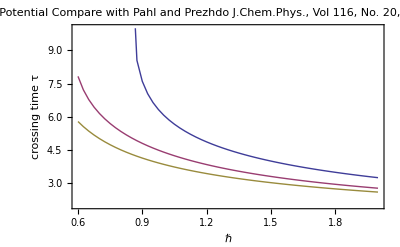

```mathematica
ListLinePlot[{data2,data3,data4},Frame->True,FrameLabel->{Style[ℏ,Large],"crossing time τ"},PlotRange->{{0.6,2},{2,10}},PlotLabel->"Decay from Metastable Potential\n Compare with Pahl and Prezhdo\n J.Chem.Phys., Vol 116, No. 20, May 2002\n Pages 8704-8712 Fig 2"]
```

## Dependence of Decay Time on po

Next commands have been written as they would be used in a different Mathematica session, using the command Get to load the hierarchy that was saved above (instead of calculating it again). Notice that the commutation relation and the Hamiltonian are defined again, and its important to use those that correspond to the hierarchy that is loaded. Next commands calculate and graph the dependence of decay time on p_0, the initial momentum, the result is used to reproduce part of a graph of the paper by Pahl and Prezhdo, see the graph below:

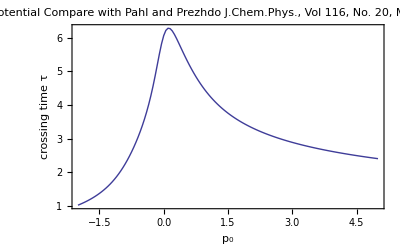

```mathematica
Needs["Quantum`QHD`"];
SetQuantumObject[q,p];
⟦q,p⟧_-=ⅈ*ℏ;
mh=p^2/(2m)+Subscript[a, 2]/2 q^2+Subscript[a, 3]/3 q^3;
hhier2=Get["qhd2.m"];
hnumhier2=hhier2/.{m->1,Subscript[a, 2]->1,Subscript[a, 3]->1/2,ℏ->1};
iniguess=1;
pdata2=Table[
hinicond2={⟨p⟩[0]==po,⟨q⟩[0]==qo,⟨q^2⟩[0]==qo^2+ℏ/(2m*ω),⟨Subscript[(p·q), 𝓈]⟩[0]==po*qo,⟨p^2⟩[0]==po^2+(ℏ*m*ω)/2}/.{qo->0,ω->1,m->1,ℏ->1};
hsol2=QHDNDSolve[hnumhier2,hinicond2,0,iniguess+0.5];
hqf2=QHDFunction[q,hsol2];
htime=(ht/.FindRoot[hqf2[ht]==-2,{ht,iniguess},AccuracyGoal->3,PrecisionGoal->3,MaxIterations->1000]);
iniguess=htime;
{po,htime},
{po,-2,5,0.05}];
ListLinePlot[pdata2,Frame->True,Axes->False,FrameLabel->{Style[Subscript[p, 0],Large],"crossing time τ"},PlotLabel->"Decay from Metastable Potential\nCompare with Pahl and Prezhdo\nJ.Chem.Phys., Vol 116, No. 20, May 2002\nPages 8704-8712 Fig 4(b)"]
```

This tutorial shows how to use the QUANTUM Mathematica add-on to reproduce the results and graphs from Pahl and Prezhdo in J. Chem Phys. Vol 116 No. 20, May 2002, Pages 8704-8712
 http://homepage.cem.itesm.mx/lgomez/quantum/QHDHigherOrders.pdf

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx